Using E2 result as an approximation for the asymmetric rectification potential

```mathematica
p1=Exp[-1/2(a+1)^2 x^2-1/2 a(a+1)y^2+a(a+1)x y];
p2=Exp[-1/2 (L/l)^2(a (L/l)^2+1)^2 x^2-1/2 a(a (L/l)^2+1)y^2+a (L/l)^2(a (L/l)^2+1)x y];
```

```mathematica
norm=π/(√a)(1/(a+1)Erf[√((a+1)/2)L]+1/((L/l)(a(L/l)^2+1))Erf[√((a(L/l)^2+1)/2)L]);
(*I am interested near the cusp. The normalisation won't be quite right close to x=0, but hopefully this is just a shift rather than a distortion of the profile near the cusp*)
```

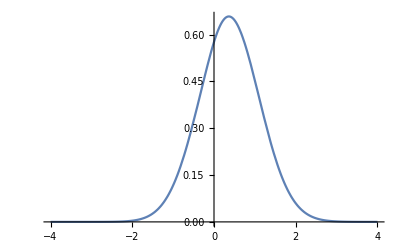

```mathematica
py=Integrate[p1,{x,0,L}]+Integrate[p2,{x,0,l}]//Simplify;
Plot[py/.{a->1,L->0.8,l->0.2},
{y,-4,4}]
(*I don't think this asymmetry is observed in simulation*)
```

```mathematica
Jp=Assuming[a>0&&L>l>0,
Integrate[y*p1/.x->L,{y,L,∞}]]//Simplify
Jm=Assuming[a>0&&L>l>0,
Integrate[y*p2/.x->-l,{y,-L^2/l,-∞}]]//Simplify
Jp/=norm;
Jm/=norm;
```

(ⅇ^(-1/2 (1+a) L^2) (2+√(a (1+a)) L √(2 π)))/(2 a (1+a))

(ⅇ^(-1/2 L^2 (1+(a L^2)/l^2)) (2 l^2+L^2 √(a (l^2+a L^2)) √(2 π)))/(2 a (l^2+a L^2))

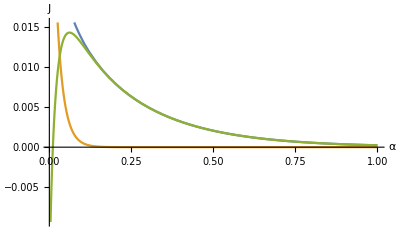

```mathematica
Plot[
{Jp,Jm,Jp-Jm}/.{L->3,l->1}//Evaluate,
{a,0,1},
PlotRange->{All,Automatic},
AxesLabel->{"α","J"}]
```

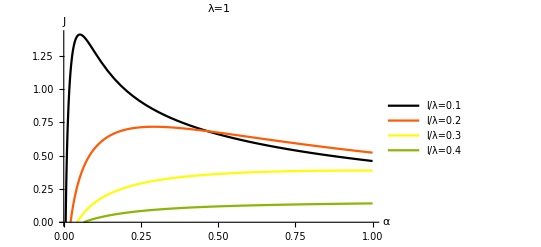

```mathematica
lam=1;
llist=Table[l,{l,0.1*lam,0.5*lam-0.1,0.1*lam}];
Jαplot=Plot[
Table[{Jp-Jm}/.{L->lam-llist[[i]],l->llist[[i]]},{i,1,Length[llist]}]//Evaluate,
{a,0,1},
PlotRange->{{0,0.5},{0,All}},
PlotLegends->Table["l/λ="<>ToString[llist[[i]]/lam],{i,1,Length[llist]}],
PlotLabel->"λ="<>ToString[lam],
AxesLabel->{"α","J"},
TicksStyle->Directive[FontSize->14],LabelStyle->Directive[FontSize->16],
PlotStyle->ColorData[3]]
Export[NotebookDirectory[]<>"/Pressure/RECT/Theory/Ja_lam"<>ToString[lam]<>".pdf",%];
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

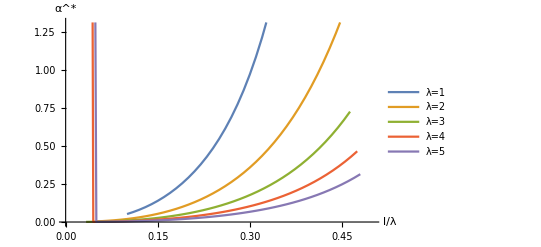

```mathematica
λlist={1,2,3,4,5};
llist=Range[Length[λlist]];
alist=Range[Length[λlist]];
For[j=1,j≤Length[λlist],j++,
λ=λlist[[j]];
llist[[j]]=Table[l,{l,0.1,0.5*λ-0.1,0.01*λ}];
alist[[j]]=Table[
a/.FindRoot[D[Jp-Jm,a]==0/.{L->λ-llist[[j,i]],l->llist[[j,i]]},{a,0.001}],
{i,1,Length[llist[[j]]]}];
llist[[j]]/=λ;
]
alplot=ListPlot[
Table[Transpose[{llist[[j]],alist[[j]]}],{j,1,Length[λlist]}],
PlotRange->{{0,0.5},{0.0,Automatic}},
AxesLabel->{"l/λ","α^*"},
PlotLegends->Table["λ="<>ToString[λlist[[j]]],{j,1,Length[λlist]}],
Joined->True]
```

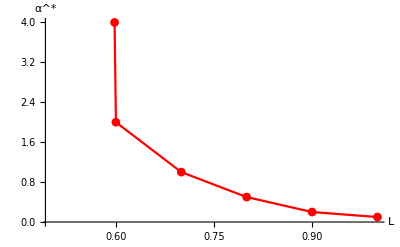

```mathematica
(*Data*)
da=ListPlot[
{{0.5,100},{0.6,2},{0.7,1},{0.8,0.5},{0.9,0.2},{1.0,0.1}},
PlotStyle->Red,
PlotRange->{All,{0.0,4}},
Joined->True,PlotMarkers->{Automatic},
AxesLabel->{"L","α^*"}]
```